```mathematica
S1=NDSolve[{-(z+1)x'[z]==-3/4 x[z] (-1+x[z]^2+3 y[z]^2),-(z+1)y'[z]==-1/4 y[z] (-9+3 x[z]^2+9 y[z]^2+0*2 √6 x[z]),x[0]==√0.27,y[0]==√0.68},{x,y},{z,0,10}];
```

```mathematica
S2=NDSolve[{-(z+1)x'[z]==-3/4 x[z] (-1+x[z]^2+3 y[z]^2),-(z+1)y'[z]==-1/4 y[z] (-9+3 x[z]^2+9 y[z]^2+0.01*2 √6 x[z]),x[0]==√0.27,y[0]==√0.68},{x,y},{z,0,10}];
```

```mathematica
S3=NDSolve[{-(z+1)x'[z]==-3/4 x[z] (-1+x[z]^2+3 y[z]^2),-(z+1)y'[z]==-1/4 y[z] (-9+3 x[z]^2+9 y[z]^2+0.05*2 √6 x[z]),x[0]==√0.27,y[0]==√0.68},{x,y},{z,0,10}];
```

```mathematica
S4=NDSolve[{-(z+1)x'[z]==-3/4 x[z] (-1+x[z]^2+3 y[z]^2),-(z+1)y'[z]==-1/4 y[z] (-9+3 x[z]^2+9 y[z]^2+0.1*2 √6 x[z]),x[0]==√0.27,y[0]==√0.68},{x,y},{z,0,10}];
```

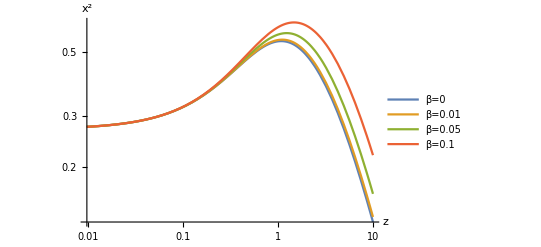

```mathematica
LogLogPlot[{Evaluate[{x[z]^2/.S1,x[z]^2/.S2,x[z]^2/.S3,x[z]^2/.S4}]},{z,0,10},PlotRange->All,PlotLegends->{"β=0","β=0.01","β=0.05","β=0.1"},AxesLabel->{HoldForm[z],HoldForm["x^2"]},LabelStyle->{FontFamily->"Latin Modern Mono",10,GrayLevel[0]}]
```

```mathematica
-x[t]^2 1/2((1-y[t]^2)/x[t]^2-1)-y[t]^2//FullSimplify
```

1/2 (-1+x[t]^2-y[t]^2)

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

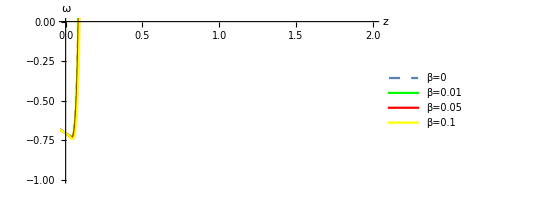

```mathematica
ParametricPlot[{Evaluate[{{Exp[-t]-1,-x[t]^2 1/2((1-y[t]^2)/x[t]^2-1)-y[t]^2}/.S1,{Exp[-t]-1,-x[t]^2 1/2((1-y[t]^2)/x[t]^2-1)-y[t]^2}/.S2,{Exp[-t]-1,-x[t]^2 1/2((1-y[t]^2)/x[t]^2-1)-y[t]^2}/.S3,{Exp[-t]-1,-x[t]^2 1/2((1-y[t]^2)/x[t]^2-1)-y[t]^2}/.S4}]},{t,-10,10},PlotRange->{{0,2},{-1,0}},PlotLegends->{"β=0","β=0.01","β=0.05","β=0.1"},AxesLabel->{HoldForm[z],HoldForm["ω"]},LabelStyle->{FontFamily->"Latin Modern Mono",10,GrayLevel[0]},PlotStyle-> {Dashed,Green,Red,Yellow}]
```

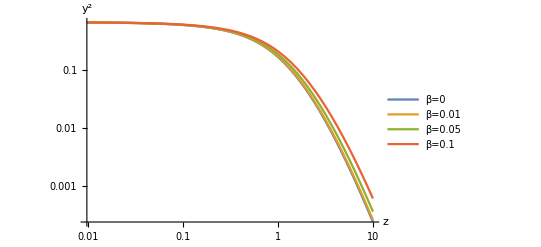

```mathematica
LogLogPlot[{Evaluate[{y[τ]^2/.S1,y[τ]^2/.S2,y[τ]^2/.S3,y[τ]^2/.S4}]},{τ,0,10},PlotRange->All,PlotLegends->{"β=0","β=0.01","β=0.05","β=0.1"},AxesLabel->{HoldForm[z],HoldForm["y^2"]},LabelStyle->{FontFamily->"Latin Modern Mono",10,GrayLevel[0]}]
```